```mathematica
OS="axion";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
Needs["PlotLegends`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
(*LS-Periodogram*)
LS[tx_, nP_] := 
 LS[tx, nP] = 
  Block[{t, x, xbar, std, τ, P, Ω, diff, lim, 
     periodogram},
    t = Table[tx[[i, 1]], {i, 1, Length[tx]}];
    x = Table[tx[[i, 2]], {i, 1, Length[tx]}];
    xbar = Mean[x];
    std = 1/(Length[x] - 1.) Sum[(x[[i]] - xbar)^2, {i, 1, Length[x]}];
    τ[ω_] := τ[ω] = ArcTan[∑_(i=1)^Length[tx] Sin[2. ω x[[i]]]/∑_(i=1)^Length[tx] Cos[2. ω x[[i]]]]/(2. ω);
    P[ω_] := P[ω] = (0.5/std) ((∑_(i=1)^Length[tx] (x[[i]]-xbar) Cos[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Cos[ω (t[[i]]-τ[ω])]^2 + (∑_(i=1)^Length[tx] (x[[i]]-xbar) Sin[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Sin[ω (t[[i]]-τ[ω])]^2);
    Ω[T_] := Ω[T] = 2. π/T;
    diff = Table[t[[i + 1]] - t[[i]], {i, 1, Length[t] - 1}]; 
    lim = Ω /@ {Last[t] - First[t], 2 Min[diff]};
    periodogram = 
     ParallelTable[{ω, P[ω]}, {ω, lim[[1]], 
       lim[[2]], (lim[[2]] - lim[[1]])/nP}]
    ];
LSCos[tx_, nP_] := 
 LSCos[tx, nP] = 
  Block[{t, x, xbar, std, τ, P, Ω, diff, lim, 
     periodogram},
    t = Table[tx[[i, 1]], {i, 1, Length[tx]}];
    x = Table[tx[[i, 2]], {i, 1, Length[tx]}];
    xbar = Mean[x];
    std = 1/(Length[x] - 1.) Sum[(x[[i]] - xbar)^2, {i, 1, Length[x]}];
    τ[ω_] := τ[ω] = ArcTan[∑_(i=1)^Length[tx] Cos[2. ω x[[i]]]/∑_(i=1)^Length[tx] Sin[2. ω x[[i]]]]/(2. ω);
    P[ω_] := P[ω] = (0.5/std) ((∑_(i=1)^Length[tx] (x[[i]]-xbar) Sin[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Sin[ω (t[[i]]-τ[ω])]^2 + (∑_(i=1)^Length[tx] (x[[i]]-xbar) Cos[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Cos[ω (t[[i]]-τ[ω])]^2);
    Ω[T_] := Ω[T] = 2. π/T;
    diff = Table[t[[i + 1]] - t[[i]], {i, 1, Length[t] - 1}]; 
    lim = Ω /@ {Last[t] - First[t], 2 Min[diff]};
    periodogram = 
     ParallelTable[{ω, P[ω]}, {ω, lim[[1]], 
       lim[[2]], (lim[[2]] - lim[[1]])/nP}]
    ];
T[periodogram_,rankmax_]:=T[periodogram,rankmax]=Block[{power,ωmax,period},power=Table[periodogram[[i,2]],{i,1,Length[periodogram]}];
ωmax=periodogram[[Position[power,RankedMax[power,rankmax]][[1,1]],1]];
{period=2 π/ωmax,RankedMax[power,rankmax]}];
p[z_,n_]:=p[z,n]=1-(1-Exp[-z])^n;
```

Working Directory: /home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online

(AscDir) Rawdata Directory: /home/prajwal/Dropbox/nEDM/rawdata

(ScrDir) Scratch Directory: /home/prajwal/Dropbox/Scratch

(PicDir) Picture Directory: /home/prajwal/Dropbox/nEDM/Pictures/nstar/runs

(SysDir) System Directory: /home/prajwal/Dropbox/nEDM/system

Rawdata on mpc1636:/xdata/nedm_data/RawData

## Making lvl3 for Sidereal

```mathematica
rundat={};
starttime=0;
pta10=pta20=fta10=fta20=erra10=erra20=fta102=fta202={};
bpt10=bft10=errb10={};
bpt20=bft20=errb20={};
bpt0=bft0=errb0={};
ptarun=Table[{},{k,1,dimdesc}];ptarun2=Table[{},{k,1,dimdesc}];
ftarun=Table[{},{k,1,dimdesc}];ftarun2=Table[{},{k,1,dimdesc}];
errarun=Table[{},{k,1,dimdesc}];errarun2=Table[{},{k,1,dimdesc}];
tsadd=2*PlusMinus[11.306,0.397];
For[i=1,i≤dimdesc,i++,
pmb0run=pmbbrun={};
If[(descdat[[i]][[5]]>20&&descdat[[i]][[5]]<9000(*&&MemberQ[{1,2,3,4,5,39,40,41},i]*))
,
(*Print[descdat[[i]][[4]]];*)
rundat=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],{Real,Real,Real,Real,Real,Real,Real,Real,Real}];
dimrundat=Dimensions[rundat][[1]];
If[i==1,starttime=rundat[[1]][[1]]];
(*For-A*tf/ts*)
ptarun[[i]]=Table[
{
Mod[(rundat[[;;,1]][[k]]-starttime)/(86164.09054),1],
{
((PlusMinus[rundat[[;;,{2,3}]][[k]][[1]],rundat[[;;,{2,3}]][[k]][[2]]])*10^6*((PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]])/(PlusMinus[descdat[[i]][[7]],0.1]+tsadd)))[[1]],
Abs[((PlusMinus[rundat[[;;,{2,3}]][[k]][[1]],rundat[[;;,{2,3}]][[k]][[2]]])*10^6*((PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]])/(PlusMinus[descdat[[i]][[7]],0.1]+tsadd)))[[2]]]
}
},
{k,1,Dimensions[rundat[[;;,{2,3}]]][[1]]}
];
ftarun[[i]]=Transpose[{ptarun[[i]][[;;,1]],ptarun[[i]][[;;,2]][[;;,1]]}];
errarun[[i]]=Abs[ptarun[[i]][[;;,2]][[;;,2]]];
(*For-A*)
ptarun2[[i]]=Table[{Mod[(rundat[[;;,1]][[k]]-starttime)/(86164.09054),1],{rundat[[;;,{2,3}]][[k]][[1]],Abs[rundat[[;;,{2,3}]][[k]][[2]]]}},{k,1,Dimensions[rundat[[;;,{2,3}]]][[1]]}];
ftarun2[[i]]=Transpose[{ptarun2[[i]][[;;,1]],ptarun2[[i]][[;;,2]][[;;,1]]}];
errarun2[[i]]=Abs[ptarun2[[i]][[;;,2]][[;;,2]]];
(**)
If[descdat[[i]][[6]]==10,
{
bpt10=Join[bpt10,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,{8,9}]]}]];
bft10=Join[bft10,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,8]]}]];
errb10=Join[errb10,rundat[[;;,9]]];
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
(*A*)
pta10=Join[pta10,ptarun[[i]]];
fta10=Join[fta10,ftarun[[i]]];
erra10=Join[erra10,errarun[[i]]];
},
{
bpt20=Join[bpt20,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,{8,9}]]}]];
bft20=Join[bft20,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,8]]}]];
errb20=Join[errb20,rundat[[;;,9]]];
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
(*A*)
pta20=Join[pta20,ptarun[[i]]];
fta20=Join[fta20,ftarun[[i]]];
erra20=Join[erra20,errarun[[i]]];
}
];
bpt0=Join[bpt0,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,{6,7}]]}]];
bft0=Join[bft0,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,6]]}]];
errb0=Join[errb0,rundat[[;;,7]]];
];
lvl3={{}};
(*Export[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3sidereal.dat"],lvl3];*)
];
```

## Combined Fit {10,20}μT

χ^2 {10,20}μT : { 3.90186 , 9.44431 }

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 0.196631 | 0.224105 | 0.877408 | 0.382738
b1 | 0.0624405 | 0.190352 | 0.328026 | 0.743699
b2 | 0.120305 | 0.316412 | 0.380215 | 0.704734
phi | -0.409704 | 0.189579 | -2.16113 | 0.0334984

{0.196631,0.0624405,0.120305,-0.409704}

{0.224105,0.190352,0.316412,0.189579}

{0.877408,0.328026,0.380215,-2.16113}

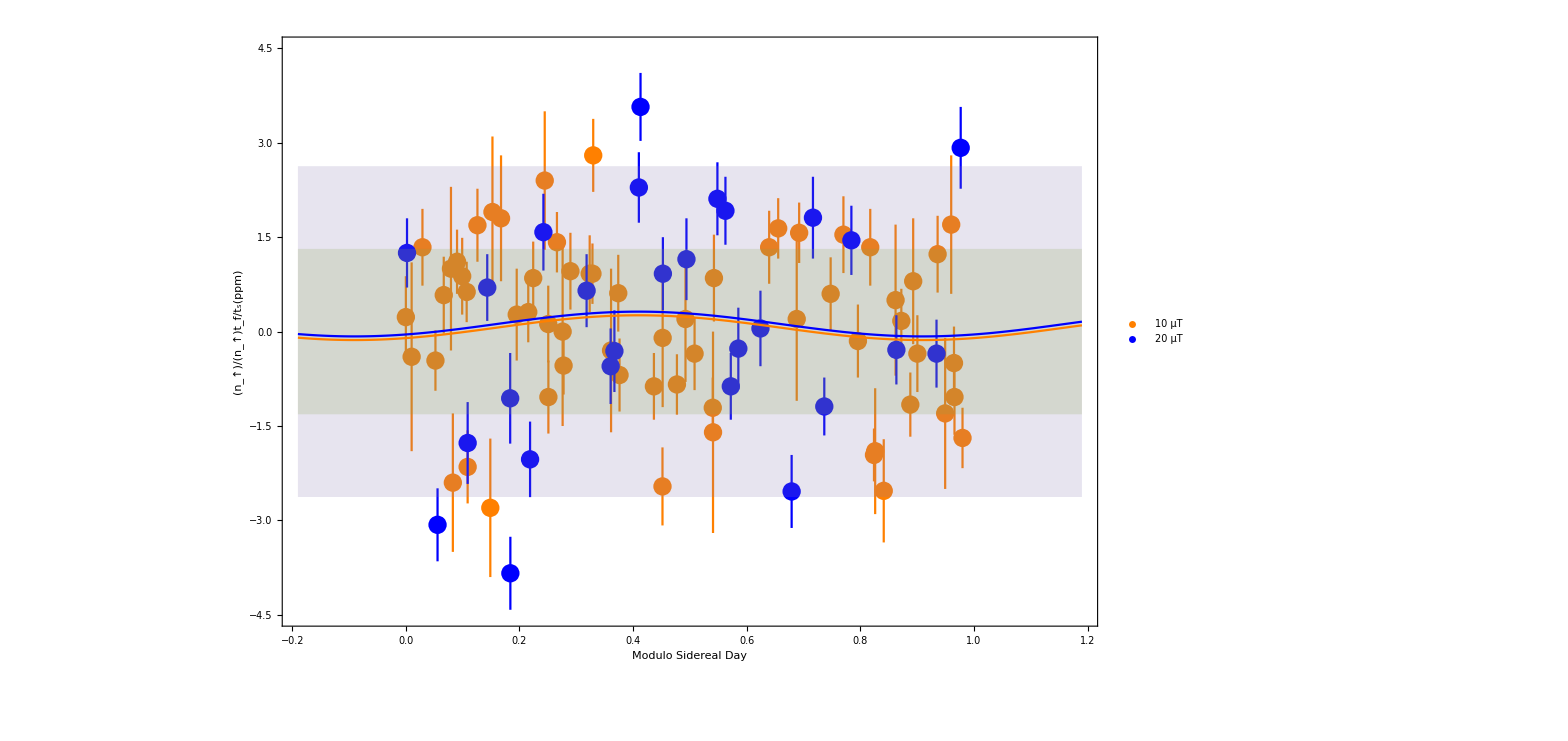

```mathematica
Clear[aa,bb,MDL];
cutoff=3;
cleanpta10=Select[pta10,Abs[#[[2]][[1]]]<cutoff&];
cleanpta20=Select[pta20,Abs[#[[2]][[1]]]<cutoff*1.5&];
cleanfta10=Table[{cleanpta10[[k]][[1]],cleanpta10[[k]][[2]][[1]]},{k,1,Dimensions[cleanpta10][[1]]}];
cleanerra10=Table[cleanpta10[[k]][[2]][[2]],{k,1,Dimensions[cleanpta10][[1]]}];
cleanfta20=Table[{cleanpta20[[k]][[1]],cleanpta20[[k]][[2]][[1]]},{k,1,Dimensions[cleanpta20][[1]]}];
cleanerra20=Table[cleanpta20[[k]][[2]][[2]],{k,1,Dimensions[cleanpta20][[1]]}];
(***)
CombiledData=Join[Insert[#,1,2]&/@cleanfta10,Insert[#,2,2]&/@cleanfta20];
Model1=a1 Cos[2Pi( t + phi)]+b1;
Model2=a1 Cos[2Pi( t+ phi)]+b2;
CombinedModel:=Which[MDL==1,Evaluate@Model1,MDL==2,Evaluate@Model2,True,0];
regreport=Quiet[NonlinearModelFit[CombiledData,
{CombinedModel,(a1>0&&a1<10^(2)&&b1>-5*10^(2)&&b1<5*10^(0)&&b2>-5*10^(0)&&b2<5*10^(0)&&phi>-1/2&&phi<1/2)},
{{a1,0.0001},{b1,0.0001},{b2,0.0001},{phi,0}},{t,MDL},Weights->Join[cleanerra10,cleanerra20],Method->NMinimize]];
Print["χ^2 {10,20}μT : { ",
N[Total[Table[((cleanfta10[[k]][[2]]-regreport[cleanfta10[[k]][[1]],1])/cleanerra10[[k]])^2,{k,1,Dimensions[cleanerra10][[1]]}]]/Dimensions[cleanerra10][[1]]]," , ",
N[Total[Table[((cleanfta20[[k]][[2]]-regreport[cleanfta20[[k]][[1]],2])/cleanerra20[[k]])^2,{k,1,Dimensions[cleanerra20][[1]]}]]/Dimensions[cleanerra20][[1]]]," }"]; 
Quiet[regreport["ParameterTable"]]
Quiet[regreport["BestFitParameters"][[;;,2]]]
Quiet[regreport["ParameterErrors"]]
Quiet[regreport["BestFitParameters"][[;;,2]]]/Quiet[regreport["ParameterErrors"]]
(***)
residual=Table[{CombiledData[[k]][[1]],regreport["FitResiduals"][[k]]},{k,1,Dimensions[CombiledData][[1]]}];
residuals=Table[{CombiledData[[k]][[1]],regreport["FitResiduals"][[k]]/Join[cleanerra10,cleanerra20][[k]]},{k,1,Dimensions[CombiledData][[1]]}];
sdcleanpta10=StandardDeviation[cleanpta10[[;;,2]][[;;,1]]];
mnpt=Show[{
EDAListPlot[cleanpta10,cleanpta20,PlotLegends->{"10 μT","20 μT"},PlotRange->{{-.19,1.19},1.5{-cutoff,cutoff}},PlotStyle->{Orange,Blue},Frame->True,FrameLabel->{"Modulo Sidereal Day","(n_↑)/(n_↑)t_f/t_s(ppm)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004]],
Plot[{regreport[t,1],regreport[t,2],sdcleanpta10,-sdcleanpta10,2sdcleanpta10,-2sdcleanpta10},{t,-.19,1.19},PlotStyle->{Orange,Blue,None,None,None,None},Filling->{{3->{4}},{5->{6}}}]
},ImageSize->1200,Frame->{True,True,True,True}]
(*Export[StringJoin[descDir,seperator,"all_lvl3sidereal.dat"],regreport["ParameterTable"][[1]][[1]][[2;;]]];*)
```

```mathematica
regreport["ParameterTable"][[1]][[1]][[2;;]]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{a1,0.196631,0.224105,0.877408,0.382738},{b1,0.0624405,0.190352,0.328026,0.743699},{b2,0.120305,0.316412,0.380215,0.704734},{phi,-0.409704,0.189579,-2.16113,0.0334984}}

## Power Spectra of A.Cos

```mathematica
DateObject[]
```

Wed 7 Mar 2018 19:19:28GMT+1.

```mathematica
(***MC***)
mcruns=1000;
np=10000;
gramftamc=Table[{},{k,1,mcruns}];
gramftamc2=Table[{},{k,1,mcruns}];
(*10*)
totdat=Join[cleanpta10,cleanpta20];
totdatft=Join[cleanfta10,cleanfta20];
For[j=1,j≤mcruns,j++,
cleanftamc={};
For[i=1,i≤Dimensions[totdat][[1]],i++,
(*RandomSeed[DateObject[]];*)
cleanftamc=AppendTo[cleanftamc,{totdat[[i]][[1]],RandomVariate[NormalDistribution[totdat[[i]][[2]][[1]],totdat[[i]][[2]][[2]]]]}];
];
gramftamc[[j]]=LS[cleanftamc,np];
gramftamc2[[j]]=LSCos[cleanftamc,np];
];//AbsoluteTiming
Show[{Periodogram[cleanftamc[[;;,2]],PlotRange->Full,PlotStyle->Blue],
Periodogram[totdat[[;;,2]][[;;,2]],PlotRange->Full,PlotStyle->Orange]
},PlotRange->{{0,.5},{-40,40}}]
gramfta=LS[totdatft,np];//AbsoluteTiming
gramfta2=LSCos[totdatft,np];
gramftamcm=Mean[gramftamc];
gramftamcm2=Mean[gramftamc2];
gramftamcs=StandardDeviation[gramftamc];
gramftamcs2=StandardDeviation[gramftamc2];
```

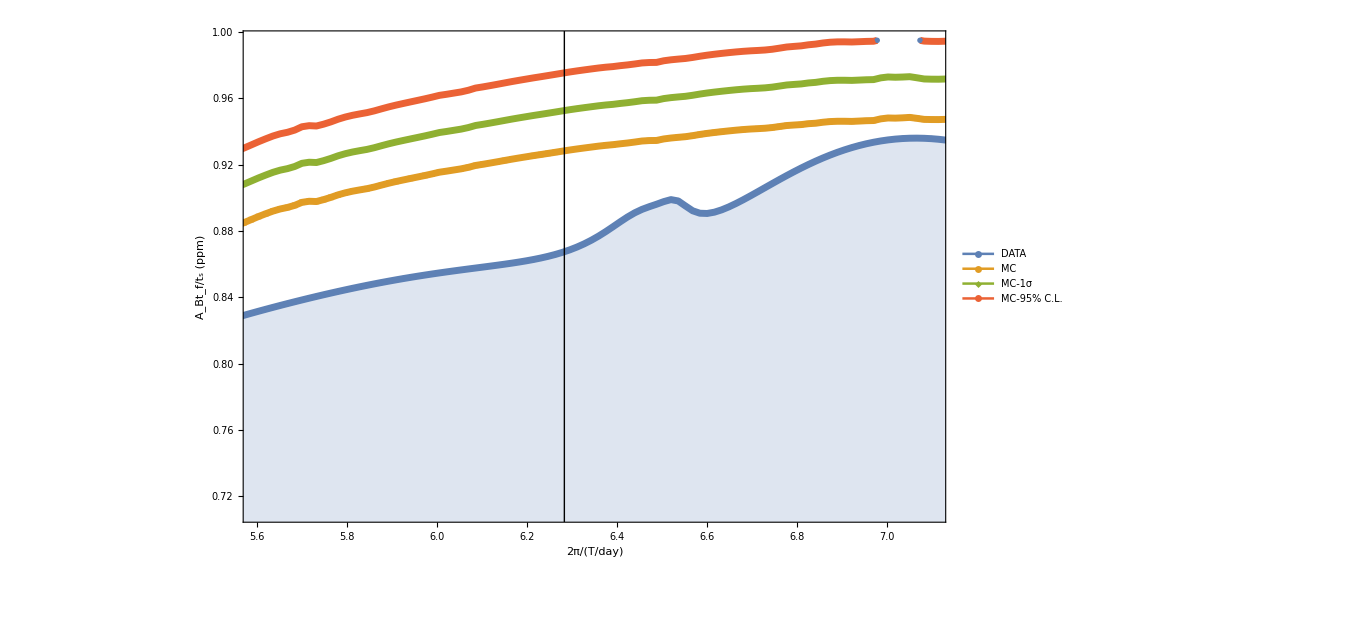

```mathematica
lineStyle={Thick,Black};
ln1=Line[{{ 2Pi,0},{2 Pi,3}}];
ptgramfta=Transpose[{gramfta[[;;,1]],Sqrt[gramfta[[;;,2]]]}];
ptgramftamcm=Transpose[{gramftamcm[[;;,1]],Sqrt[gramftamcm[[;;,2]]]}];
ptgramftamcm1=Transpose[{gramfta[[;;,1]],Sqrt[gramftamcm[[;;,2]]+gramftamcs[[;;,2]]/Sqrt[2 mcruns]]}];
ptgramftamcm95=Transpose[{gramfta[[;;,1]],Sqrt[gramftamcm[[;;,2]]+1.96 gramftamcs[[;;,2]]/Sqrt[2 mcruns]]}];
ptgramfta2=Transpose[{gramfta2[[;;,1]],Sqrt[gramfta2[[;;,2]]]}];
ptgramftamcm2=Transpose[{gramftamcm2[[;;,1]],Sqrt[gramftamcm2[[;;,2]]]}];
ptgramftamcm12=Transpose[{gramfta2[[;;,1]],Sqrt[gramftamcm2[[;;,2]]+gramftamcs2[[;;,2]]/Sqrt[2 mcruns]]}];
ptgramftamcm952=Transpose[{gramfta2[[;;,1]],Sqrt[gramftamcm2[[;;,2]]+1.96 gramftamcs2[[;;,2]]/Sqrt[2 mcruns]]}];
ptgramftap=Transpose[{gramfta2[[;;,1]],ArcTan[Sqrt[gramfta[[;;,2]]/gramfta2[[;;,2]]]]}];
ptgramftamcmp=Transpose[{gramftamcm2[[;;,1]],ArcTan[Sqrt[gramftamcm[[;;,2]]/gramftamcm2[[;;,2]]]]}];
ptgramftamcm1p=Transpose[{gramfta2[[;;,1]],ArcTan[Sqrt[gramftamcm[[;;,2]]+gramftamcs[[;;,2]]]/Sqrt[gramftamcm2[[;;,2]]+gramftamcs2[[;;,2]]]]}];
ptgramftamcm95p=Transpose[{gramfta2[[;;,1]],ArcTan[Sqrt[gramftamcm[[;;,2]]+1.96 gramftamcs[[;;,2]]]/Sqrt[gramftamcm2[[;;,2]]+1.96 gramftamcs2[[;;,2]]]]}];
ListPlot[{ptgramfta,ptgramftamcm,ptgramftamcm1,ptgramftamcm95},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,0},PlotRange->{{5.6,7.1},{.71,.995}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{ptgramfta2,ptgramftamcm2,ptgramftamcm12,ptgramftamcm952},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,0},PlotRange->{{5.6,7.1},{.71,.995}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{Sqrt[ptgramfta^2+ptgramfta2^2]/Sqrt[2],Sqrt[ptgramftamcm^2+ptgramftamcm2^2]/Sqrt[2],Sqrt[ptgramftamcm1^2+ptgramftamcm12^2]/Sqrt[2],Sqrt[ptgramftamcm95^2+ptgramftamcm952^2]/Sqrt[2]},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,0},PlotRange->{{5.6,7.1},{.71,.995}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{ptgramftap,ptgramftamcmp,ptgramftamcm1p,ptgramftamcm95p},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","ϕ"},PlotMarkers->{Automatic,0},PlotRange->{{5.6,7.1},{.71,.995}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
```

```mathematica
interdat=Interpolation[ptgramfta];
intermc=Interpolation[ptgramftamcm];
intermc1=Interpolation[ptgramftamcm1];
intermc95=Interpolation[ptgramftamcm95];
interdat[2Pi]-PlusMinus[intermc[2Pi],-intermc[2Pi]+intermc1[2Pi]]
```

-0.061±0.024

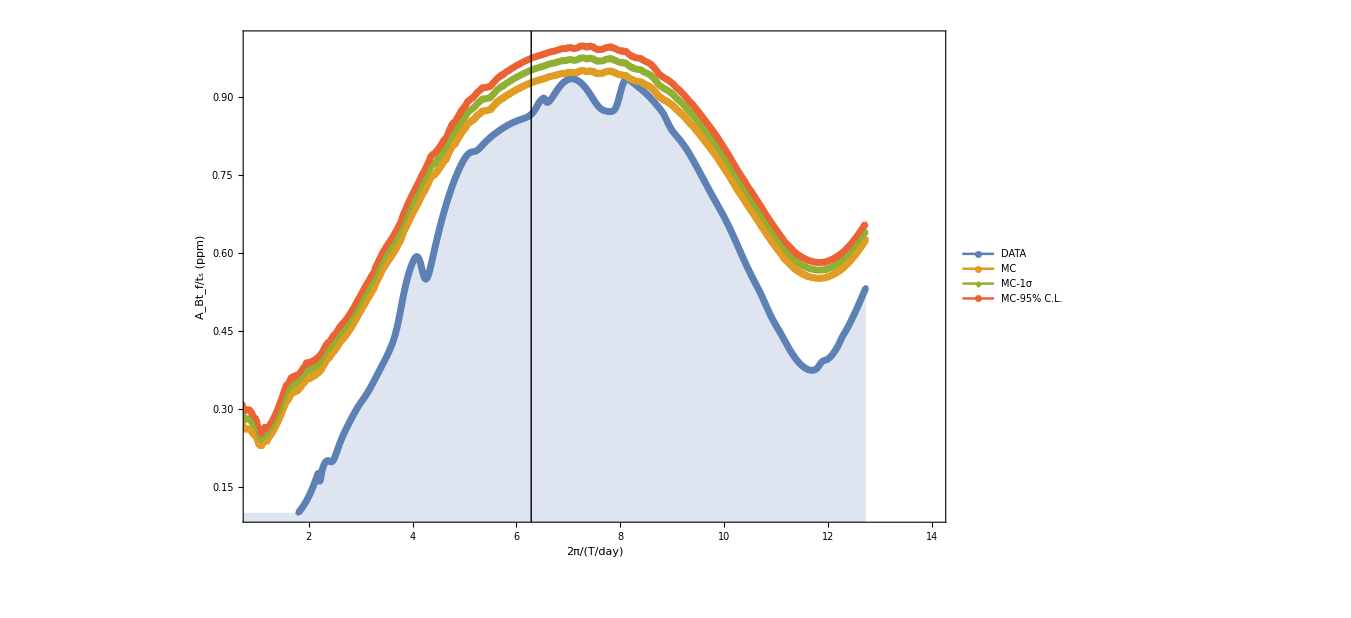

```mathematica
ListPlot[{ptgramfta,ptgramftamcm,ptgramftamcm1,ptgramftamcm95},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{1,11},{.1,.99}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{ptgramfta2,ptgramftamcm2,ptgramftamcm12,ptgramftamcm952},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,0},PlotRange->{{1,11},{.1,.99}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{Sqrt[ptgramfta^2+ptgramfta2^2]/Sqrt[2],Sqrt[ptgramftamcm^2+ptgramftamcm2^2]/Sqrt[2],Sqrt[ptgramftamcm1^2+ptgramftamcm12^2]/Sqrt[2],Sqrt[ptgramftamcm95^2+ptgramftamcm952^2]/Sqrt[2]},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,0},PlotRange->{{1,11},{.1,.99}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{ptgramftap,ptgramftamcmp,ptgramftamcm1p,ptgramftamcm95p},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","ϕ"},PlotMarkers->{Automatic,0},PlotRange->{{1,11},{0.65,.9}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
```

## Test